```mathematica
(1-a)p+a q
```

(1-a) p+a q

```mathematica
ExpandAll[Out[1]]
```

p-a p+a q

```mathematica
(1-a) p+a q/.{p->{t,t},q->{Cos[t],Sin[t]}}
```

{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}

```mathematica
Manipulate[
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
},{t,0,2π}]
,{a,0,1}]
```

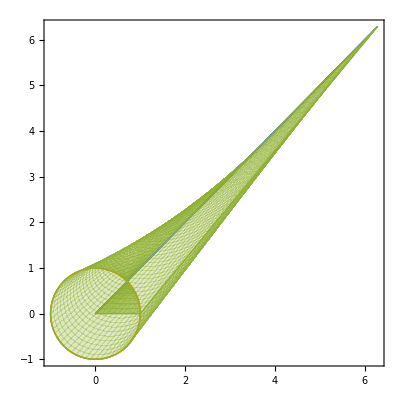

```mathematica
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
},{t,0,2π},{a,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
},{t,0,2π},{a,0,b}]
,{b,0,1}]
```

```mathematica
({(1-a) t+a Cos[t],(1-a) t+a Sin[t]}/.a->1)-({(1-a) t+a Cos[t],(1-a) t+a Sin[t]}/.a->0)
```

{-t+Cos[t],-t+Sin[t]}

```mathematica
Norm@{-t+Cos[t],-t+Sin[t]}
```

√(Abs[-t+Cos[t]]^2+Abs[-t+Sin[t]]^2)

```mathematica
√((-t+Cos[t])^2+(-t+Sin[t])^2)
```

√((-t+Cos[t])^2+(-t+Sin[t])^2)

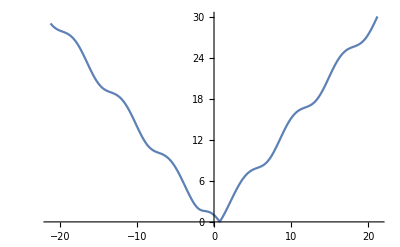

```mathematica
Plot[√((-t+Cos[t])^2+(-t+Sin[t])^2),{t,-21.205750411731103,21.205750411731103}]
```

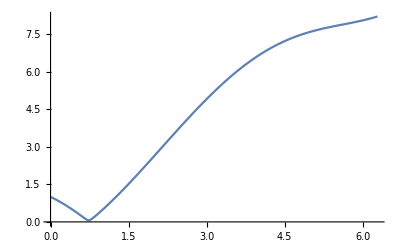

```mathematica
Plot[√((-t+Cos[t])^2+(-t+Sin[t])^2),{t,0,2π}]
```

```mathematica
Curl[{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{t,a}]
```

1-a+t-Cos[t]+a Cos[t]

```mathematica
Manipulate[Plot[1-a+t-Cos[t]+a Cos[t],{t,0,2π}],{a,0,1}]
```

```mathematica
Plot3D[1-a+t-Cos[t]+a Cos[t],{t,0,2π},{a,0,1}]
```

-Graphics3D-

```mathematica
(√(1+f'[x]))/x
```

(√(1+f'[x]))/x

```mathematica
D[(√(1+f'[x]))/x,f[x]]-D[D[(√(1+f'[x]))/x,f'[x]],x]==0
```

1/(2 x^2 √(1+f'[x]))+f''[x]/(4 x (1+f'[x])^(3/2))==0

```mathematica
DSolve[1/(2 x^2 √(1+f'[x]))+f''[x]/(4 x (1+f'[x])^(3/2))==0,{f[x],f[x]},{x}]
```

{{f[x]→-x-C[1]/x+C[2]}}

```mathematica
-x-1/x
```

-1/x-x

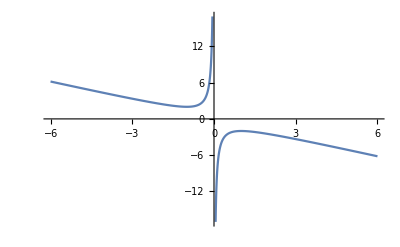

```mathematica
Plot[-1/x-x,{x,-6.0120000000000005,6.0120000000000005}]
```

```mathematica
f'[x]-f[x]
```

-f[x]+f'[x]

```mathematica
∫_Subscript[x, 1]^Subscript[x, 2] f'[x]-f[x]ⅆx
```

```mathematica
∫_0^1 2x-x^2 ⅆx
```

```mathematica
∫_0^1 (2x-x^2)ⅆxIntegrate[1==a √(1-Cos[x]^2),x]
```

2/3

```mathematica
∫_0^1 (f'[x]-f[x])ⅆx
```

∫_0^1 (-f[x]+f'[x])ⅆx

```mathematica
∫_0^1 (f''[x]-f'[x])ⅆx
```

∫_0^1 (-f'[x]+f''[x])ⅆx

```mathematica
Dt[∫_0^1 (f''[x]-f'[x])ⅆx]
```

0

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
Nest[Dt,f[x],1]
```

Dt[x] f'[x]

```mathematica
Nest[Dt,f[x],2]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
Nest[Dt,f[x],3]
```

Dt[Dt[Dt[x]]] f'[x]+3 Dt[x] Dt[Dt[x]] f''[x]+Dt[x]^3 f^(3)[x]

```mathematica
Nest[Dt,f[x],5]
```

Dt[Dt[Dt[Dt[Dt[x]]]]] f'[x]+10 Dt[Dt[x]] Dt[Dt[Dt[x]]] f''[x]+5 Dt[x] Dt[Dt[Dt[Dt[x]]]] f''[x]+15 Dt[x] Dt[Dt[x]]^2 f^(3)[x]+10 Dt[x]^2 Dt[Dt[Dt[x]]] f^(3)[x]+10 Dt[x]^3 Dt[Dt[x]] f^(4)[x]+Dt[x]^5 f^(5)[x]

```mathematica
Integrate[√(1-x^2),x]
```

1/2 (x √(1-x^2)+ArcSin[x])

```mathematica
Nest[Dt,f[x],2]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
Nest[Dt,f[x],3]
```

Dt[Dt[Dt[x]]] f'[x]+3 Dt[x] Dt[Dt[x]] f''[x]+Dt[x]^3 f^(3)[x]

```mathematica
Integrate[√(1-x^2),x]
```

1/2 (x √(1-x^2)+ArcSin[x])

```mathematica
Integrate[1/(√(1-x^2)),x]
```

ArcSin[x]

```mathematica
Integrate[1/(√(1-Cos[x]^2)),x]
```

((-Log[Cos[x/2]]+Log[Sin[x/2]]) Sin[x])/(√(Sin[x]^2))

```mathematica
1/(√(1-Cos[x]^2))√(1-Cos[x]^2)==a √(1-Cos[x]^2)
```

1==a √(1-Cos[x]^2)

```mathematica
Integrate[1==a √(1-Cos[x]^2),x]
```

∫(1==a √(1-Cos[x]^2))ⅆx

```mathematica
Integrate[1,x]==Integrate[a √(1-Cos[x]^2),x]
```

x==-a Cot[x] √(Sin[x]^2)

```mathematica
Reduce[x==-a Cot[x] √(Sin[x]^2)]
```

(√(1-Cos[2 x]) Cot[x]≠0&&a==-(√2 x Tan[x])/(√(1-Cos[2 x])))||x==0

```mathematica
D[√((-t+Cos[t])^2+(-t+Sin[t])^2),t]==0
```

(2 (-t+Cos[t]) (-1-Sin[t])+2 (-1+Cos[t]) (-t+Sin[t]))/(2 √((-t+Cos[t])^2+(-t+Sin[t])^2))==0

```mathematica
Reduce[(2 (-t+Cos[t]) (-1-Sin[t])+2 (-1+Cos[t]) (-t+Sin[t]))/(2 √((-t+Cos[t])^2+(-t+Sin[t])^2))==0]
```

Reduce[(2 (-t+Cos[t]) (-1-Sin[t])+2 (-1+Cos[t]) (-t+Sin[t]))/(2 √((-t+Cos[t])^2+(-t+Sin[t])^2))==0]

```mathematica
FindMinimum[√((-t+Cos[t])^2+(-t+Sin[t])^2),{t,1}]
```

{0.0647013,{t→0.733196}}

```mathematica
0.7331955522957041
```

```mathematica
(2 (-t+Cos[t]) (-1-Sin[t])+2 (-1+Cos[t]) (-t+Sin[t]))/(2 √((-t+Cos[t])^2+(-t+Sin[t])^2))/.t->0.7331955522957041
```

1.63478×10^-10

```mathematica
Norm@{I,1}
```

√2

```mathematica
{I,1}
```

{ⅈ,1}

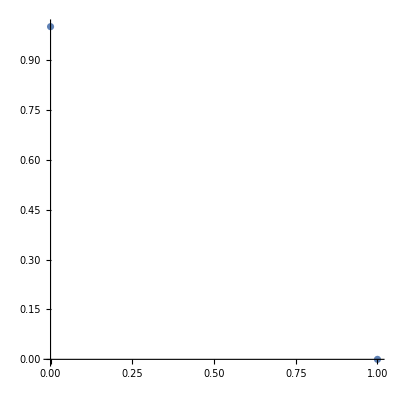

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{ⅈ,1},AspectRatio->1]
```

```mathematica
Dt[f[g[x]]]==Dt[g[f[x]]]
```

Dt[x] f'[g[x]] g'[x]==Dt[x] f'[x] g'[f[x]]

```mathematica
Dt[Dt[x] f'[g[x]] g'[x]==Dt[x] f'[x] g'[f[x]]]
```

Dt[Dt[x]] f'[g[x]] g'[x]+Dt[x]^2 g'[x]^2 f''[g[x]]+Dt[x]^2 f'[g[x]] g''[x]==Dt[Dt[x]] f'[x] g'[f[x]]+Dt[x]^2 g'[f[x]] f''[x]+Dt[x]^2 f'[x]^2 g''[f[x]]

```mathematica
FullForm[Dt[Dt[x]] f'[g[x]] g'[x]+Dt[x]^2 g'[x]^2 f''[g[x]]+Dt[x]^2 f'[g[x]] g''[x]==Dt[Dt[x]] f'[x] g'[f[x]]+Dt[x]^2 g'[f[x]] f''[x]+Dt[x]^2 f'[x]^2 g''[f[x]]]
```

Equal[Plus[Times[Dt[Dt[x]],Derivative[1][f][g[x]],Derivative[1][g][x]],Times[Power[Dt[x],2],Power[Derivative[1][g][x],2],Derivative[2][f][g[x]]],Times[Power[Dt[x],2],Derivative[1][f][g[x]],Derivative[2][g][x]]],Plus[Times[Dt[Dt[x]],Derivative[1][f][x],Derivative[1][g][f[x]]],Times[Power[Dt[x],2],Derivative[1][g][f[x]],Derivative[2][f][x]],Times[Power[Dt[x],2],Power[Derivative[1][f][x],2],Derivative[2][g][f[x]]]]]

```mathematica
TraditionalForm[Dt[Dt[x]] f'[g[x]] g'[x]+Dt[x]^2 g'[x]^2 f''[g[x]]+Dt[x]^2 f'[g[x]] g''[x]==Dt[Dt[x]] f'[x] g'[f[x]]+Dt[x]^2 g'[f[x]] f''[x]+Dt[x]^2 f'[x]^2 g''[f[x]]]
```

(ⅆx)^2 (g'(x))^2 f''(g(x))+(ⅆx)^2 g''(x) f'(g(x))+ⅆ(ⅆx) g'(x) f'(g(x))==(ⅆx)^2 f''(x) g'(f(x))+(ⅆx)^2 (f'(x))^2 g''(f(x))+ⅆ(ⅆx) f'(x) g'(f(x))

```mathematica
FullSimplify[Dt[Dt[x] f'[g[x]] g'[x]==Dt[x] f'[x] g'[f[x]]]]
```

Dt[Dt[x]] (f'[g[x]] g'[x]-f'[x] g'[f[x]])+Dt[x]^2 (-g'[f[x]] f''[x]+g'[x]^2 f''[g[x]]+f'[g[x]] g''[x]-f'[x]^2 g''[f[x]])==0

```mathematica
ParametricPlot3D[{
{(1-a) t+a Cos[t],(1-a) t+a Sin[t],a}
},{t,0,2π},{a,0,1}]
```

-Graphics3D-

```mathematica
{(1-a) t+a Cos[t],(1-a) t+a Sin[t],a}/.a->1
```

{Cos[t],Sin[t],1}

```mathematica
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}/.a->1
```

{Cos[t],Sin[t]}

```mathematica
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}/.a->0
```

{t,t}

```mathematica
{Cos[t],Sin[t]}-{t,t}
```

{-t+Cos[t],-t+Sin[t]}

```mathematica
Norm@{-t+Cos[t],-t+Sin[t]}
```

√(Abs[-t+Cos[t]]^2+Abs[-t+Sin[t]]^2)

```mathematica
FullSimplify[Norm@{-t+Cos[t],-t+Sin[t]},t∈Reals]
```

√(1+2 t^2-2 t (Cos[t]+Sin[t]))

```mathematica
Plot[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,-21.205750411731103,21.205750411731103}]
```

-Graphics-

```mathematica
f[√(1+2 t^2-2 t (Cos[t]+Sin[t]))]==α 7
```

f[√(1+2 t^2-2 t (Cos[t]+Sin[t]))]==7 α

```mathematica
Integrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),t]
```

∫√(1+2 t^2-2 t (Cos[t]+Sin[t]))ⅆt

```mathematica
NIntegrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),t]
```

NIntegrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),t]

```mathematica
NIntegrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

28.9736

```mathematica
NIntegrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

```mathematica
∫_0^1 ∫_0^(2π) {(1-a) t+a Cos[t],(1-a) t+a Sin[t]}ⅆtⅆa
```

{π^2,π^2}

```mathematica
Norm[∫_0^1 ∫_0^(2π) {(1-a) t+a Cos[t],(1-a) t+a Sin[t]}ⅆtⅆa]
```

√2 π^2

```mathematica
N[√2 π^2]
```

13.9577

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
(π^2)^2
```

π^4

```mathematica
N[π^4]
```

97.4091

```mathematica
{1,2}-{3,4}
```

{-2,-2}

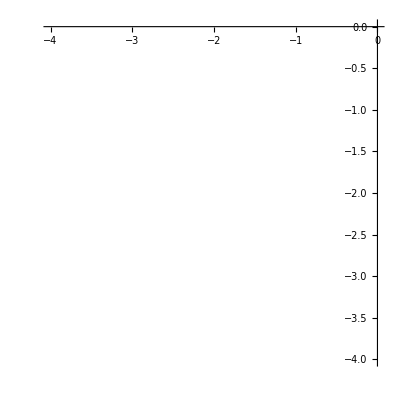

```mathematica
Show[{
ParametricPlot[
{-2,-2}
,{t,-2,2}],
ListPlot[{{1,2},{3,4}}]
}]
```

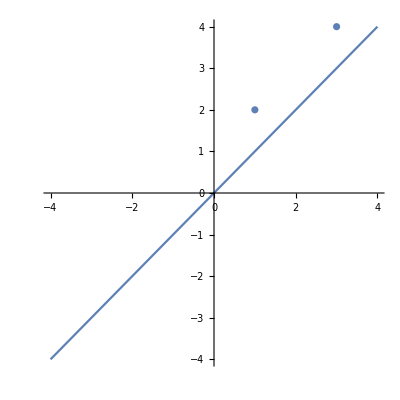

```mathematica
Show[{
ParametricPlot[
{-2t,-2t}
,{t,-2,2}],
ListPlot[{{1,2},{3,4}}]
}]
```

```mathematica
Solve[{y[1]==2,y[3]==4},{y[x]},x]
```

{}

```mathematica
Solve[{y[1]==2,y[3]==4},{y[x]},x]
```

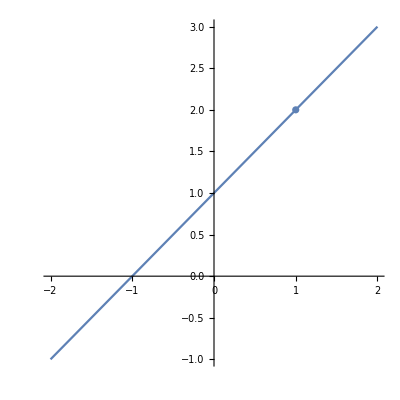

```mathematica
Show[{
ParametricPlot[
{t,t+1}
,{t,-2,2}],
ListPlot[{{1,2},{3,4}}]
}]
```

```mathematica
SurfaceData["Cylinder","ParametricEquations"]
```

Function[a,Function[{u,v},{a Cos[u],a Sin[u],v}]]

```mathematica
SurfaceData["Cylinder","ParametricEquations"][1][θ,ϕ]
```

{Cos[θ],Sin[θ],ϕ}

```mathematica
Show[{
ParametricPlot[
{t,t+1}
,{t,-2,2}],
ListPlot[{{1,2},{3,4}}]
}]
```

```mathematica
ParametricPlot3D[
{Cos[θ],Sin[θ],ϕ}
,{θ,0,2π},{ϕ,0,2π}
]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{Cos[θ],Sin[θ],ϕ},
{}
},{θ,0,2π},{ϕ,0,2π}
]
```

```mathematica
{Cos[θ],Sin[θ],ϕ}/.{θ->t,ϕ->t+1}
```

{Cos[t],Sin[t],1+t}

```mathematica
ParametricPlot3D[{
{Cos[θ],Sin[θ],ϕ},
{Cos[θ],Sin[θ],1+θ}
},{θ,0,2π},{ϕ,0,2π}
]
```

-Graphics3D-

```mathematica
{Cos[t],Sin[t],1+t}/.t->0
```

{1,0,1}

```mathematica
{Cos[t],Sin[t],1+t}/.t->1
```

{Cos[1],Sin[1],2}

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
Dt[f[x],2]
```

Dt[f[x],2]

```mathematica
Dt[f[x],x]
```

f'[x]

```mathematica
Dt@Dt[f[x]]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
FullForm[Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]]
```

Plus[Times[Dt[Dt[x]],Derivative[1][f][x]],Times[Power[Dt[x],2],Derivative[2][f][x]]]

```mathematica
TraditionalForm[Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]]
```

(ⅆx)^2 f''(x)+ⅆ(ⅆx) f'(x)

```mathematica
Dt@Dt[f[x]]==g''[x]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]==g''[x]

```mathematica
Solve[Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]==g''[x],f'[x]]
```

{{f'[x]→(-Dt[x]^2 f''[x]+g''[x])/Dt[Dt[x]]}}

```mathematica
TraditionalForm@((-Dt[x]^2 f''[x]+g''[x])/Dt[Dt[x]])
```

(g''(x)-(ⅆx)^2 f''(x))/(ⅆ(ⅆx))

```mathematica
f'[x]Dt[Dt[x]]==-Dt[x]^2 f''[x]+g''[x]
```

Dt[Dt[x]] f'[x]==-Dt[x]^2 f''[x]+g''[x]

```mathematica
TraditionalForm[f'[x]Dt[Dt[x]]==-Dt[x]^2 f''[x]+g''[x]]
```

ⅆ(ⅆx) f'(x)==g''(x)-(ⅆx)^2 f''(x)

```mathematica
Dt[Dt[t]]==Dt[√(1+2 t^2-2 t (Cos[t]+Sin[t]))]
```

Dt[Dt[t]]==(4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))

```mathematica
Dt[f[t]]==√(1+2 t^2-2 t (Cos[t]+Sin[t]))
```

Dt[t] f'[t]==√(1+2 t^2-2 t (Cos[t]+Sin[t]))

```mathematica
Dt[Dt[f[t]]]==Dt[√(1+2 t^2-2 t (Cos[t]+Sin[t]))]
```

Dt[Dt[t]] f'[t]+Dt[t]^2 f''[t]==(4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))

```mathematica
Solve[Dt[Dt[t]] f'[t]+Dt[t]^2 f''[t]==(4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t]))),f'[t]]
```

{{f'[t]→(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) f''[t])/(Dt[Dt[t]] √(1+2 t^2-2 t Cos[t]-2 t Sin[t]))}}

```mathematica
Dt[Dt[f[t]]]==√(1+2 t^2-2 t (Cos[t]+Sin[t]))
```

Dt[Dt[t]] f'[t]+Dt[t]^2 f''[t]==√(1+2 t^2-2 t (Cos[t]+Sin[t]))

```mathematica
Solve[Dt[Dt[t]] f'[t]+Dt[t]^2 f''[t]==√(1+2 t^2-2 t (Cos[t]+Sin[t])),f'[t]]
```

{{f'[t]→(√(1+2 t^2-2 t Cos[t]-2 t Sin[t])-Dt[t]^2 f''[t])/Dt[Dt[t]]}}

```mathematica
TraditionalForm@((√(1+2 t^2-2 t Cos[t]-2 t Sin[t])-Dt[t]^2 f''[t])/Dt[Dt[t]])
```

(√(2 t^2-2 t sin(t)-2 t cos(t)+1)-(ⅆt)^2 f''(t))/(ⅆ(ⅆt))

```mathematica
D[√(1+2 t^2-2 t (Cos[t]+Sin[t])),t]
```

(4 t-2 t (Cos[t]-Sin[t])-2 (Cos[t]+Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))

```mathematica
((4 t-2 t (Cos[t]-Sin[t])-2 (Cos[t]+Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t]))))^2
```

(4 t-2 t (Cos[t]-Sin[t])-2 (Cos[t]+Sin[t]))^2/(4 (1+2 t^2-2 t (Cos[t]+Sin[t])))

```mathematica
(√(1+2 t^2-2 t Cos[t]-2 t Sin[t])-Dt[t]^2 ((4 t-2 t (Cos[t]-Sin[t])-2 (Cos[t]+Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))))/Dt[Dt[t]]
```

(√(1+2 t^2-2 t Cos[t]-2 t Sin[t])-(Dt[t]^2 (4 t-2 t (Cos[t]-Sin[t])-2 (Cos[t]+Sin[t])))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t]))))/Dt[Dt[t]]

```mathematica
FullSimplify[(√(1+2 t^2-2 t Cos[t]-2 t Sin[t])-(Dt[t]^2 (4 t-2 t (Cos[t]-Sin[t])-2 (Cos[t]+Sin[t])))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t]))))/Dt[Dt[t]],t∈Reals∧Dt[t]==1]
```

ComplexInfinity

```mathematica
FullSimplify[(√(1+2 t^2-2 t Cos[t]-2 t Sin[t])-(Dt[t]^2 (4 t-2 t (Cos[t]-Sin[t])-2 (Cos[t]+Sin[t])))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t]))))/Dt[Dt[t]],t∈Reals]
```

(1+2 t^2-2 t (Cos[t]+Sin[t])+Dt[t]^2 (-2 t+(1+t) Cos[t]+Sin[t]-t Sin[t]))/(Dt[Dt[t]] √(1+2 t^2-2 t (Cos[t]+Sin[t])))

```mathematica
Dt[f[t]]==√(1+2 t^2-2 t (Cos[t]+Sin[t]))
```

Dt[t] f'[t]==√(1+2 t^2-2 t (Cos[t]+Sin[t]))

```mathematica
Dt[Dt[f[t]]]==Dt[√(1+2 t^2-2 t (Cos[t]+Sin[t]))]
```

Dt[Dt[t]] f'[t]+Dt[t]^2 f''[t]==(4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))

```mathematica
TraditionalForm@Dt[Dt[t]] f'[t]+Dt[t]^2 f''[t]==(4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))
```

ⅆ(ⅆt) f'[t]+Dt[t]^2 f''[t]==(4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))

```mathematica
TraditionalForm[Dt[Dt[t]] f'[t]+Dt[t]^2 f''[t]==(4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))]
```

(ⅆt)^2 f''(t)+ⅆ(ⅆt) f'(t)==(4 t ⅆt-2 ⅆt (sin(t)+cos(t))-2 t (ⅆt cos(t)-ⅆt sin(t)))/(2 √(2 t^2-2 t (sin(t)+cos(t))+1))

```mathematica
Solve[
Dt[Dt[t]] f'[t]+Dt[t]^2 f''[t]==(4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))
,f''[t]]
```

{{f''[t]→(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-Dt[Dt[t]] √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) f'[t])/(Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]))}}

```mathematica
Solve[
Dt[Dt[t]] f'[t]+Dt[t]^2 f''[t]==(4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))
,f'[t]]
```

{{f'[t]→(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) f''[t])/(Dt[Dt[t]] √(1+2 t^2-2 t Cos[t]-2 t Sin[t]))}}

```mathematica
(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) f''[t])/(Dt[Dt[t]] √(1+2 t^2-2 t Cos[t]-2 t Sin[t]))
```

```mathematica
TraditionalForm[f'[t]==(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) f''[t])/(Dt[Dt[t]] √(1+2 t^2-2 t Cos[t]-2 t Sin[t]))]
```

f'(t)==((ⅆt)^2 f''(t) (-√(2 t^2-2 t sin(t)-2 t cos(t)+1))+2 t ⅆt+t ⅆt sin(t)-ⅆt sin(t)-t ⅆt cos(t)-ⅆt cos(t))/(ⅆ(ⅆt) √(2 t^2-2 t sin(t)-2 t cos(t)+1))

```mathematica
(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) f''[t])/(Dt[Dt[t]] √(1+2 t^2-2 t Cos[t]-2 t Sin[t]))/.f''[t]->(4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t]))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))
```

(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-(Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) (4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t])))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t]))))/(Dt[Dt[t]] √(1+2 t^2-2 t Cos[t]-2 t Sin[t]))

```mathematica
TraditionalForm@Out@113
```

(-((ⅆt)^2 √(2 t^2-2 t sin(t)-2 t cos(t)+1) (4 t ⅆt-2 ⅆt (sin(t)+cos(t))-2 t (ⅆt cos(t)-ⅆt sin(t))))/(2 √(2 t^2-2 t (sin(t)+cos(t))+1))+2 t ⅆt+t ⅆt sin(t)-ⅆt sin(t)-t ⅆt cos(t)-ⅆt cos(t))/(ⅆ(ⅆt) √(2 t^2-2 t sin(t)-2 t cos(t)+1))

```mathematica
Solve[f'[t]== 
(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-(Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) (4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t])))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t]))))/(Dt[Dt[t]] √(1+2 t^2-2 t Cos[t]-2 t Sin[t])),f'[t]Dt[Dt[t]] ]
```

Solve[f'[t]==(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-(Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) (4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t])))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t]))))/(Dt[Dt[t]] √(1+2 t^2-2 t Cos[t]-2 t Sin[t])),Dt[Dt[t]] f'[t]]

```mathematica
MultiplySides[f'[t]==(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-(Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) (4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t])))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t]))))/(Dt[Dt[t]] √(1+2 t^2-2 t Cos[t]-2 t Sin[t])),Dt[Dt[t]]]
```

Piecewise[{{Dt[Dt[t]] f'[t]==1/(√(1+2 t^2-2 t Cos[t]-2 t Sin[t]))(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-(Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) (4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t])))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))), Dt[Dt[t]]≠0}, {f'[t]==1/(Dt[Dt[t]] √(1+2 t^2-2 t Cos[t]-2 t Sin[t]))(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-(Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) (4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t])))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t])))), True}}]

```mathematica
TraditionalForm[Dt[Dt[t]] f'[t]==1/(√(1+2 t^2-2 t Cos[t]-2 t Sin[t]))(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-(Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) (4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t])))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t]))))]
```

ⅆ(ⅆt) f'(t)==(-((ⅆt)^2 √(2 t^2-2 t sin(t)-2 t cos(t)+1) (4 t ⅆt-2 ⅆt (sin(t)+cos(t))-2 t (ⅆt cos(t)-ⅆt sin(t))))/(2 √(2 t^2-2 t (sin(t)+cos(t))+1))+2 t ⅆt+t ⅆt sin(t)-ⅆt sin(t)-t ⅆt cos(t)-ⅆt cos(t))/(√(2 t^2-2 t sin(t)-2 t cos(t)+1))

```mathematica
ExpandAll@(2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-Dt[t] Sin[t]+t Dt[t] Sin[t]-(Dt[t]^2 √(1+2 t^2-2 t Cos[t]-2 t Sin[t]) (4 t Dt[t]-2 Dt[t] (Cos[t]+Sin[t])-2 t (Cos[t] Dt[t]-Dt[t] Sin[t])))/(2 √(1+2 t^2-2 t (Cos[t]+Sin[t]))))
```

2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-2 t Dt[t]^3+Cos[t] Dt[t]^3+t Cos[t] Dt[t]^3-Dt[t] Sin[t]+t Dt[t] Sin[t]+Dt[t]^3 Sin[t]-t Dt[t]^3 Sin[t]

```mathematica
Dt[Dt[t]]f'[t]==2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-2 t Dt[t]^3+Cos[t] Dt[t]^3+t Cos[t] Dt[t]^3-Dt[t] Sin[t]+t Dt[t] Sin[t]+Dt[t]^3 Sin[t]-t Dt[t]^3 Sin[t]
```

Dt[Dt[t]] f'[t]==2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-2 t Dt[t]^3+Cos[t] Dt[t]^3+t Cos[t] Dt[t]^3-Dt[t] Sin[t]+t Dt[t] Sin[t]+Dt[t]^3 Sin[t]-t Dt[t]^3 Sin[t]

```mathematica
TraditionalForm@Dt[Dt[t]] f'[t]==2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-2 t Dt[t]^3+Cos[t] Dt[t]^3+t Cos[t] Dt[t]^3-Dt[t] Sin[t]+t Dt[t] Sin[t]+Dt[t]^3 Sin[t]-t Dt[t]^3 Sin[t]
```

ⅆ(ⅆt) f'[t]==2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-2 t Dt[t]^3+Cos[t] Dt[t]^3+t Cos[t] Dt[t]^3-Dt[t] Sin[t]+t Dt[t] Sin[t]+Dt[t]^3 Sin[t]-t Dt[t]^3 Sin[t]

```mathematica
TraditionalForm[Dt[Dt[t]] f'[t]==2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-2 t Dt[t]^3+Cos[t] Dt[t]^3+t Cos[t] Dt[t]^3-Dt[t] Sin[t]+t Dt[t] Sin[t]+Dt[t]^3 Sin[t]-t Dt[t]^3 Sin[t]]
```

ⅆ(ⅆt) f'(t)==-2 t (ⅆt)^3+2 t ⅆt-t (ⅆt)^3 sin(t)+(ⅆt)^3 sin(t)+t ⅆt sin(t)-ⅆt sin(t)+t (ⅆt)^3 cos(t)+(ⅆt)^3 cos(t)-t ⅆt cos(t)-ⅆt cos(t)

```mathematica
Integrate[Integrate[Integrate[-2t,t],t],t]
```

-t^4/12

```mathematica
Integrate[Integrate[Integrate[2t,t],t],t]
```

t^4/12

```mathematica
Solve[Dt[Dt[t]] f'[t]==2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-2 t Dt[t]^3+Cos[t] Dt[t]^3+t Cos[t] Dt[t]^3-Dt[t] Sin[t]+t Dt[t] Sin[t]+Dt[t]^3 Sin[t]-t Dt[t]^3 Sin[t],f[t]]
```

{}

```mathematica
DSolve[Dt[Dt[t]] f'[t]==2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-2 t Dt[t]^3+Cos[t] Dt[t]^3+t Cos[t] Dt[t]^3-Dt[t] Sin[t]+t Dt[t] Sin[t]+Dt[t]^3 Sin[t]-t Dt[t]^3 Sin[t],f[t]]
```

DSolve[Dt[Dt[t]] f'[t]==2 t Dt[t]-Cos[t] Dt[t]-t Cos[t] Dt[t]-2 t Dt[t]^3+Cos[t] Dt[t]^3+t Cos[t] Dt[t]^3-Dt[t] Sin[t]+t Dt[t] Sin[t]+Dt[t]^3 Sin[t]-t Dt[t]^3 Sin[t],f[t]]